# First Return y'=f(y) e.g. y_1==0

The VDP system and the Rosseler system both cross y_1==0 repeatedly.  The first return map (fory_1==0) is a natural way to look at the behavior of the system as a map from the plane y_1=0 onto the plane y_1=0.

We are going to look at this first for the 2D VDP problem and then see how much messier it gets for the 3D Roseller system.

First Return Map (Informal Definition)
The first return map for an ODE y'=f(y) on a surface 𝒮  is where the solution of the  ODE first returns to the surface 𝒮   (in the same direction) as a function on 𝒮.

## First Return Map for VDP System y_1==0

Our VDP system is
	y1' | = | y2                               
y2' | = | μ(1-y1^2)y2-y1
I am going to look at initial conditions y_0=(0,x) and catch the output y_*=(0,r(x)) the first time it crosses y_1==0 heading in the same direction. In Mathematica there is a way to catch values from the ODE solver when it locates an event.

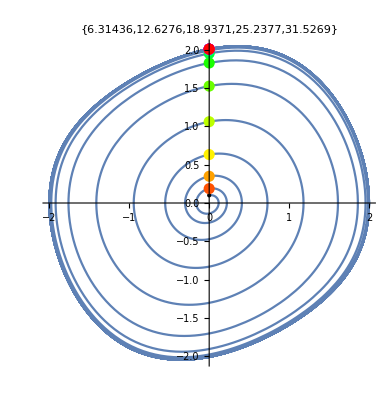

```mathematica
f[μ_][{x_,v_}]:={v,μ (1-x^2)v-x}
Df[μ_][{x_,v_}]:={{0,1},{-1-2v x μ,μ (1-x^2)}}
TMax=124.5;y0={0,.1};μ=0.2; ϵ=1;
{Hmm,{Data}}=Reap[{ySol,JSol}=NDSolveValue[{
y'[t]==f[μ][y[t]],y[0]==y0,
J'[t]==Df[μ][y[t]].J[t],J[0]=={{1,0},{0,1}}
},{y,J},{t,0, TMax},
Method->{"EventLocator", "Event":>y[t]⟦1⟧==0,"Direction"->1,
"EventAction":> Sow[{t, y[t], J[t]}]}];
];
ParametricPlot[ySol[t],{t,0, TMax},
Epilog->{{Black,Point[ySol[0]]},Table[{Hue[i/Length[Data]],PointSize[0.02],Point[Data⟦i,2⟧]},{i,Length[Data]}]},
PlotLabel->Data⟦1;;5,1⟧]
```

## First Return Map for Rosseller System y_1==0

The same trick for the  Rosseler system.

```mathematica
Clear[ f,df,y1,y2,y3,a,b,c]
f[{a_,b_,c_}][{y1_,y2_,y3_}]:= {-y2-y3,y1+ a y2, b  + y3(y1-c)}
df[{a_,b_,c_}][{y1_,y2_,y3_}]:={{0,-1,-1},{1,a,0},{y3,0,-c+y1}}
StdParams={0.2,0.2,5.7};  TMax=54;
y0={0,1.7,14.6};
{Hmm,{Data}}=Reap[{ySol,JSol}=NDSolveValue[{
y'[t]==f[StdParams][y[t]],y[0]==y0,
J'[t]==df[StdParams][y[t]].J[t], J[0]==({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})
},{y,J},{t,0, TMax},
Method->{"EventLocator", "Event":>y[t]⟦1⟧==0,"Direction"->1,
"EventAction":> Sow[{t, y[t], J[t]}]}];
];
BasePic=Show[
ParametricPlot3D[ySol[t],{t,0, TMax},
PlotRange->All],
Graphics3D[{Black,PointSize[0.02],Point[ySol[0]]}],
Graphics3D[{Opacity[0.5],Yellow,Polygon[15{{0,-1,0},{0,1,0},{0,1,2},{0,-1,2}}]}]];
Dots=Graphics3D[{PointSize[0.02],Table[{Hue[i/Length[Data]],Point[Data⟦i,2⟧]},{i,Length[Data]}]},
Axes->True,BoxRatios->{1, 1, 1}];
TabView[{
"y"->BasePic,
"y+"->Show[BasePic,Dots,PlotLabel->Data⟦All,1⟧],
"Dots"->Dots
}]
```

123

## Plotting Functions of 2 Variables

```mathematica
f[{x1_,x2_}]:={x1 + 0.1x2 x1 ,x2+0.2Sin[x1 x2]}
TabView[{
"In"->ParametricPlot[{x1,x2},{x1,-2,2},{x2,-2,2},
Mesh->Automatic],
"Out"->ParametricPlot[f[{x1,x2}],{x1,-2,2},{x2,-2,2},
Mesh->Automatic]
}]
```

12